### Mathematica Hw III

Claus Ernst/Huanjing Wang		Math/Cs 371 Spring 2016
Due: Wednesday, February 17 before class.  
This assignment must be turned in electronically AND as a hard copy.  The electronic copy must be submitted through blackboard prior to your class.

#### General Requirements - read before you start working

Form groups of two. Each member of the group must understand and be able to explain (in detail) all of the code turned in. We allow you to work in groups so that you have someone with whom you can talk about your work in detail. This is not meant for group members to only do half of the work. 

Each group turns in one (stapled) printout at the beginning of class and submits an electronic copy (one file) prior to class.

Your electronic and hard copy must include: 
a) The names of both group members on the print out (printed from the file, not added by hand). The name of both group members must be included in the name of the electronic file. For example if we (Claus and Huanjing) are a team then the file name should be ErnstWang371Hw3.nb. This will help to identify whose file we are looking at and it will also avoid having several different files with the same name.
b) A solution to each problem, which includes the code, as well as a couple of executions of your code which demonstrate that the code is (most likely) correct. Select different types of input for your example runs, to show that different parts of your code work correctly.   
Your solutions must be well-documented Mathematica code, that is, you must use comments, meaningful variable names, proper indentations, hide local variables (if any are needed), etc.  The comments in the code should be such that taken by themselves they describe the algorithm you used.

Note: Throughout this assignment, the lists of arguments for functions are given to clarify the order and meaning of the arguments; they do not follow Mathematica syntax. However, your solutions must follow the given order/structure of arguments as specified by the assignment. If you do deviate from this our test programs will not run.

### Problem 1: Geometry and Circles

Given a circle with center (0,0) and radius R. Assume that we want to put n≥3 small circles of radius r on the outside of the big circle such that they are just touching and are tangent to each other. 
(i) 	(a) Derive a formula for the radius r in terms of n and R.
	(b) Derive a formula for the centers of the small circles in terms of n and R.
(ii) Write a function CircleRing[R,n] that draws the big circle in black together with the n small circles in red. Below is an example:
CircleRing[5,15]

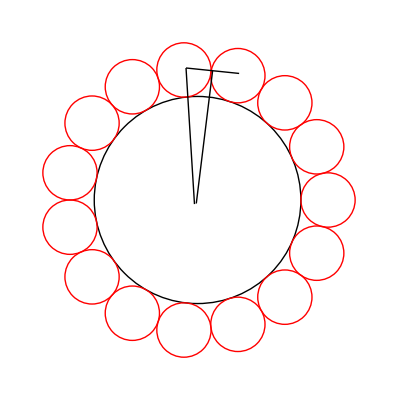

(iii) Let n_1,n_2, be two positive integers greater or equal to three.
Write a function TwoCircleRings[R,n_1,n_2] that does the following:
	- draws a black circle of radius R
	- surrounds the circle if radius R with n_1 small circles in blue as in the previous part.
	- draws an even bigger circle surrounding all the circles
	- surrounds the big circle with  n_2 small circles in red as in the previous part.
	- draws an even bigger circle surrounding the whole thing.
For example: 
TwoCircleRings[4,7,15]

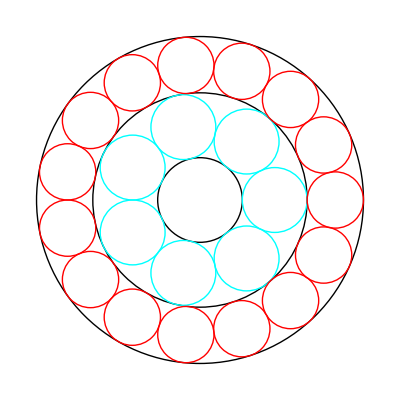

(iv) Let integerlst={n_1,n_2,...,n_k} be a list of positive integers, n_i≥3.
Write a function kCircleRings[R,integerlst] that iterated the previous construction.
Note that all the small circles need to have different colors.
For example
kCircleRings[4,{7,25,34,52,100}]

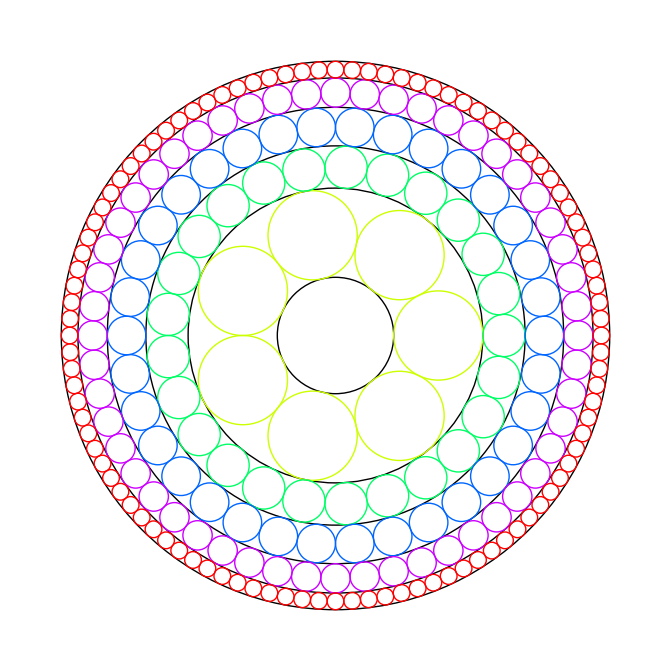

### Problem 2: A number investigation

(i) Write a function Digitssquare [x] which takes an integer value x and returns the sum of the digit squares. For example, given the number 76543, the function should return 135 
(135=7^2+6^2+5^2+4^2+3^2)

(ii) We now define a sequence by x_(i+1)=Digitssquare [x_i] with a starting value x_1 (Assume x_1 is a positive integer)
For example if x_1=76543 then x_2=135 and x_3=35 and x_4=34 and so on.
Write a function DigitssquareSequence[x_1,n] that returns a list of the first n elements of such a sequence, i.e {x_1,x_2,...,x_n}.
For example DigitssquareSequence[76543,4] returns {76543,135,35,34}.

Your task will be to investigate what happens to such sequences. This is an open ended problem and requires an in-depth investigation.
Hint: You might want to write some helper functions to do this investigation:
For example write a function that can detect if such a sequence starts to repeat.

(iii) Make at least five statements about either the Digitssquare process or about the sequences it generates.

(iv) Prove at least one of your five statements above.

(v) Extra credit: Repeat the above except you use cubes. For example Digitscube[123] =1+8+27= 36.